## Physics 449 hw#3

Name: Ruojun Wang
Due: 2018/2/16 W4F

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## 1) Townsend 10.7

```mathematica
Integrate[r^2 ⅇ^(-3 r/a0),{r,0,∞}]
```

ConditionalExpression[(2 a0^3)/27,Re[a0]>0]

```mathematica
8*64/27^2
```

512/729

```mathematica
N[512/729]
```

0.702332

## 5) What is the degeneracy and parity of the 17/2ℏω energy levels of the 3d isotropic harmonic oscillator? Calculate the wavefunction of the l=5 state.

Given by (10.90~10.93), u=ρ^(l+1)ⅇ^(-ρ^2/2)f(ρ), f(ρ)≃(∑^∞ c_k ρ^k≃ⅇ^(ρ^2))_(k=0), ρ=√((μ ω)/ℏ)r→ ψ=(u(r))/r Y_(l,m)(θ,ϕ)=1/r(√((μ ω)/ℏ)r)^(5+1)ⅇ^(-(√((μ ω)/ℏ)r)^2/2)ⅇ^((√((μ ω)/ℏ)r)^2)Y_(5,m)(θ,ϕ)

```mathematica
Table[1/r(√((μ ω)/ℏ)r)^(5+1)ⅇ^(-(√((μ ω)/ℏ)r)^2/2)ⅇ^((√((μ ω)/ℏ)r)^2)SphericalHarmonicY[5,m,θ,ϕ],{m,-5,5}]//Simplify
```

{(3 ⅇ^(-5 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(77/π) r^5 μ^3 ω^3 Sin[θ]^5)/(32 ℏ^3),(3 ⅇ^(-4 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(385/(2 π)) r^5 μ^3 ω^3 Cos[θ] Sin[θ]^4)/(16 ℏ^3),(ⅇ^(-3 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(385/π) r^5 μ^3 ω^3 (7+9 Cos[2 θ]) Sin[θ]^3)/(64 ℏ^3),(ⅇ^(-2 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(1155/(2 π)) r^5 μ^3 ω^3 Cos[θ] (1+3 Cos[2 θ]) Sin[θ]^2)/(16 ℏ^3),(ⅇ^(-ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(165/(2 π)) r^5 μ^3 ω^3 (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(16 ℏ^3),(ⅇ^((r^2 μ ω)/(2 ℏ)) √(11/π) r^5 μ^3 ω^3 Cos[θ] (15-70 Cos[θ]^2+63 Cos[θ]^4))/(16 ℏ^3),-(ⅇ^(ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(165/(2 π)) r^5 μ^3 ω^3 (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(16 ℏ^3),(ⅇ^(2 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(1155/(2 π)) r^5 μ^3 ω^3 Cos[θ] (1+3 Cos[2 θ]) Sin[θ]^2)/(16 ℏ^3),-(ⅇ^(3 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(385/π) r^5 μ^3 ω^3 (7+9 Cos[2 θ]) Sin[θ]^3)/(64 ℏ^3),(3 ⅇ^(4 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(385/(2 π)) r^5 μ^3 ω^3 Cos[θ] Sin[θ]^4)/(16 ℏ^3),-(3 ⅇ^(5 ⅈ ϕ+(r^2 μ ω)/(2 ℏ)) √(77/π) r^5 μ^3 ω^3 Sin[θ]^5)/(32 ℏ^3)}

## 7) Townsend 12.4

```mathematica
Integrate[(N ⅇ^(-α x^2))^2,{x,-∞,∞}]
```

ConditionalExpression[(N^2 √(π/2))/(√α),Re[α]>0]

```mathematica
Solve[(N^2 √(π/2))/(√α)==1,N]
```

{{N→-(2/π)^(1/4) α^(1/4)},{N→(2/π)^(1/4) α^(1/4)}}

```mathematica
ψT2=(2/π)^(1/4) α^(1/4)ⅇ^(-α x^2);
KE=-ℏ^2/(2m) D[ψT2,{x,2}]//Simplify
```

-(ⅇ^(-x^2 α) (2/π)^(1/4) α^(5/4) (-1+2 x^2 α) ℏ^2)/m

```mathematica
Energy7=Integrate[ψT2(KE+b x^4 ψT2),{x,-∞,∞}]
```

ConditionalExpression[(3 b m+8 α^3 ℏ^2)/(16 m α^2),Re[α]>0]

```mathematica
DEnergy7=D[Energy7,{α,1}]//Simplify
```

ConditionalExpression[-(3 b)/(8 α^3)+ℏ^2/(2 m),Re[α]>0]

```mathematica
Solve[-(3 b)/(8 α^3)+ℏ^2/(2 m)==0,α]
```

{{α→-((-3)^(1/3) b^(1/3) m^(1/3))/(2^(2/3) ℏ^(2/3))},{α→(3^(1/3) b^(1/3) m^(1/3))/(2^(2/3) ℏ^(2/3))},{α→((-1)^(2/3) 3^(1/3) b^(1/3) m^(1/3))/(2^(2/3) ℏ^(2/3))}}

```mathematica
Energy7b=(3 b)/(16 ((3^(1/3) b^(1/3) m^(1/3))/(2^(2/3) ℏ^(2/3)))^2)+((3^(1/3) b^(1/3) m^(1/3))/(2^(2/3) ℏ^(2/3)) ℏ^2)/(2 m)//Simplify//N
```

(0.68142 b^(1/3) ℏ^(4/3))/m^(2/3)

```mathematica
4^(1/3)(0.6814202223120523 b^(1/3) ℏ^(4/3))/m^(2/3)
```

(1.08169 b^(1/3) ℏ^(4/3))/m^(2/3)

## 8) Townsend 12.6

### a)

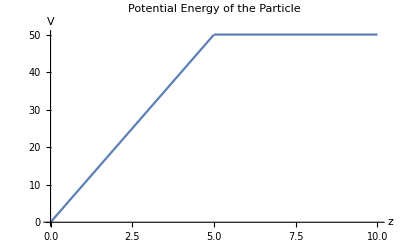

```mathematica
VPlot=Plot[Piecewise[{{10z,z<5},{50,z>5}}],{z,0,10}]

Show[VPlot,AxesLabel->{HoldForm[z],HoldForm[V]},PlotLabel->HoldForm[Potential Energy of the Particle],LabelStyle->{GrayLevel[0]}]
```

```mathematica
ψ8=C z ⅇ^(- α z);
Integrate[ψ8^2,{z,0,∞}]
```

ConditionalExpression[C^2/(4 α^3),Re[α]>0]

```mathematica
Solve[C^2/(4 α^3)==1,C]
```

{{C→-2 α^(3/2)},{C→2 α^(3/2)}}

```mathematica
ψ8b=2 α^(3/2) z ⅇ^(- α z);
```

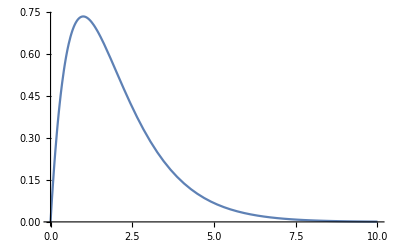

```mathematica
Plot[2 z ⅇ^(- z),{z,0,10}]
```

### b)

```mathematica
D2ψ8b=D[ψ8b,{z,2}]
```

-4 ⅇ^(-z α) α^(5/2)+2 ⅇ^(-z α) z α^(7/2)

```mathematica
ExpH8=Integrate[ψ8b*(-ℏ^2/(2m)D2ψ8b-m g z ψ8b),{z,0,∞}]
```

ConditionalExpression[-(3 g m)/(2 α)+(α^2 ℏ^2)/(2 m),Re[α]>0]

```mathematica
D1ExpH8=D[-(3 g m)/(2 α)+(α^2 ℏ^2)/(2 m),{α,1}]
```

(3 g m)/(2 α^2)+(α ℏ^2)/m

```mathematica
Solve[(3 g m)/(2 α^2)+(α ℏ^2)/m==0,α]
```

{{α→((-3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3)},{α→-((3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3)},{α→-((-1)^(2/3) (3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3)}}

```mathematica
ε1=-(3 g m)/(2 (-((3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3)))+((-((3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3))^2 ℏ^2)/(2 m)//Simplify//N
```

1.96556 g^(2/3) m^(1/3) ℏ^(2/3)

### c)

```mathematica
ExpZ=Integrate[ψ8b*(-z ψ8b),{z,0,∞}]
```

ConditionalExpression[-3/(2 α),Re[α]>0]

```mathematica
3/(2 ((3/2)^(1/3) g^(1/3) m^(2/3))/ℏ^(2/3))//N
```

(1.31037 ℏ^(2/3))/(g^(1/3) m^(2/3))